```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]; 
Needs["HierarchicalClustering`"]
SetOptions[MatrixPlot,ImageSize->300{1,1}];
```

NDSolveValue::mxsst: Using maximum number of grid points 1200 allowed by the MaxPoints or MinStepSize options for independent variable x$3296.

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolveValue::ndcf: Repeated convergence test failure at t$3296 == 0.; unable to continue.

NDSolveValue::mxsst: Using maximum number of grid points 1200 allowed by the MaxPoints or MinStepSize options for independent variable x$3296.

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolveValue::ndcf: Repeated convergence test failure at t$3296 == 0.; unable to continue.

InterpolatingFunction::dmval: Input value {2000., 0.00191577} lies outside the range of data in the interpolating function. Extrapolation will be used.

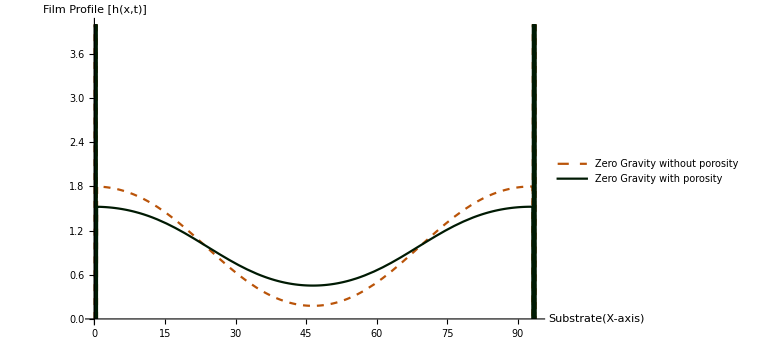

```mathematica
Module[{j=2.,k = 0.0677,xMin=0,xMax=2*(Pi/0.067),TMax=2000.,Bi=1.,M=35.1,Pr=7.02, Ga=0.,Pm=0.3,S=100.,u,t,x,mult},
mult=0.;
hSol= NDSolveValue[{D[u[t, x], t] == (-100)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         5*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}];

mult=1.;
hSolp= NDSolveValue[{D[u[t, x], t] == (-100)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         5*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}];

Plot[{hSol[TMax,x],hSolp[TMax,x]},{x,xMin,xMax},PlotRange->{0,4},BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel->{"Substrate(X-axis)","Film Profile [h(x,t)]"},ImageSize->Large,PlotStyle->{{Thick,Dashed,RGBColor[0.73,0.33,0.034]},{Thick,RGBColor[0.,0.1,0.01]}},PlotLegends->{"Zero Gravity without porosity","Zero Gravity with porosity"}]]
```